```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/code"];
```

```mathematica
Num=100000;
data = Partition[ReadList["!./a.out bootstrap.dat " <> ToString[Num], Number],4];
a=data[[All,1]];
b=data[[All,2]];
c=data[[All,3]];
chisq=data[[All,4]];
```

16381.3

0.896785

-4.90884

10.0245

0.231385

0.179564

0.0288612

0.0103101

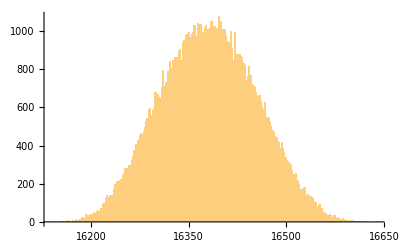

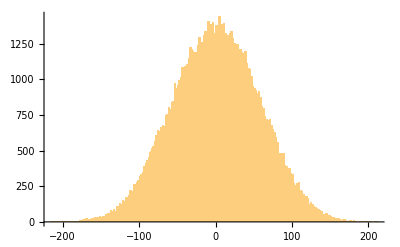

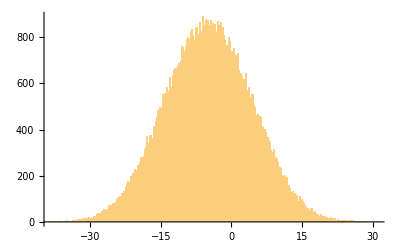

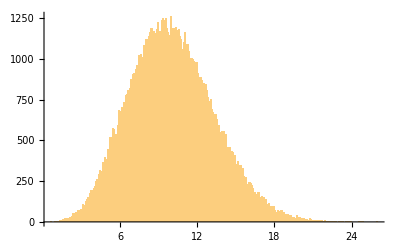

```mathematica
Mean[a]
Mean[b]
Mean[c]
Mean[chisq]
StandardDeviation[a]/Sqrt[Num]
StandardDeviation[b]/Sqrt[Num]
StandardDeviation[c]/Sqrt[Num]
StandardDeviation[chisq]/Sqrt[Num]
Histogram[a,200]
Histogram[b,200]
Histogram[c,200]
Histogram[chisq,200]
```

```mathematica
raw = ReadList["bootstrap.dat",{Number, Number}];
```

```mathematica
refined = raw[[2;;]];
```

```mathematica
Mean[Partition[refined[[All,2]],13][[All,1]]]
Mean[Partition[refined[[All,2]],13][[All,1]]]
```

16381.3

16381.3